```mathematica
Выполнил: Фомин Константин Анатольевич БПИ155;
Mod[Plus@@ToCharacterCode["Фомин Константин Анатольевич , 155"],18]+1
```

13

```mathematica
Задание 1;

f[x_] = (√(x^4  + 5))/(x + 5);
(*Найдём промежутки знакопостояннства *)
Reduce[f[x] < 0,x]
Reduce[f[x] > 0,x]

(*Найдём промежутки монотонности *)
Reduce[f'[x] > 0,x]  // N(* f[x] возрастает *)
Reduce[f'[x] < 0,x]  // N(* f[x] убывает*)

(*Найдём точки перегиба *)
Solve[f''[x] == 0,x] // N

(* Точек перегиба нет, тк корни - комплексные числа *)
(* Найдём промежутки выпуклости *)
Reduce[f''[x] < 0,x]
(* Найдём промежутки вогнутости *)
Reduce[f''[x] > 0,x] 

(* x = -5 вертикальная асимптота, тк в ней функция не определена *)

k = Limit[f[x]/x,x -> Infinity] (* коэффициент k асимптоты *)

b = Limit[f[x] - k*x, x  -> Infinity] (* коэффициент b асимптоты *)

y = k*x + b (* уравнение асимптоты *)

(*Графическая иллюстрация (зелёная прямая - вертикальная асимптота, ораньжевая - наклонная*)
Show[{Plot[{f[x],x-5},{x,-25,25}],ContourPlot[x == -5,{x,-25,25},{y,-70,70},ContourStyle -> Green]}]
```

x<-5

x>-5

x<-10.005||x>0.774215

-10.005<x<-5.||-5.<x<0.774215

{{x→-1.36055-1.16954 ⅈ},{x→-1.36055+1.16954 ⅈ},{x→0.00886521-0.257741 ⅈ},{x→0.00886521+0.257741 ⅈ},{x→1.35168-1.6864 ⅈ},{x→1.35168+1.6864 ⅈ}}

x<-5

x>-5

1

-5

-5+x

x==-0.781288||x==2.30058

-2.≤x<-0.781288||2.30058<x≤4.

-40-1/ⅇ^8+ⅇ^4

20+1/ⅇ^2-ⅇ^4

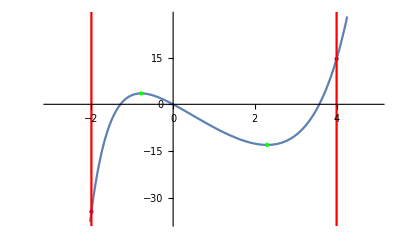

```mathematica
Задание 2;
ClearAll[f,a,b,k,y,x];
f[x_] = E^x -  E^(-2x) - 10x;
a = -2;
b = 4;
(* отрезок - [-2,4] *)
Reduce[f'[x] == 0 && x ≥ -2 && x ≤ 4,x] // N  (* стационарные точки на этом промежутке *)
Reduce[f'[x] > 0 && x ≥ -2 && x ≤ 4,x] // N (* промежутки, где функция возрастает (для того чтобы определить стационарные точки на максимум и минимум *)
Xmax = -0.781288;
Xmin = 2.30058;
Max[f[Xmax],f[b]]  (* берем точку локального максимума и правую границу - большее из этих чисел - наибольшее значение функции на промежутке [a,b] (тк к ней функция возрастает)  *)
(* х = 4 *)
Min[f[Xmin],f[a]] (* аналогично с наименьшим знач. : выбираем левую границу и точку локального минимума *)
(* X = -2 *)
(* нарисуем экстремумы и точки наибольших и наименьших значений
   (зеленые точки - экстремумы, фиолетовые - точки наим. и наиб. значений, красные линии - отрезок [a,b] *)
Show[{
Plot[f[x],{x,-3,5}],Graphics[{PointSize->Large,Green,Point[{{Xmin,f[Xmin]},{Xmax,f[Xmax]}}]}],Graphics[{PointSize->Large,Purple,Point[{{a,f[a]},{b,f[b]}}]}] ,ContourPlot[{ x == a, x == b},{x,-10,10},{y,-50,50},ContourStyle-> Red]
}]
```

```mathematica
Задание 3;
ClearAll[f,x,y]
f[x_,y_] = -5 - x - 3 x^2 - 3y - y^2;
x0 = -2;
y0 = -2;
M = {x0,y0,f[x0,y0]}
dFx = D[f[x,y],x] /. {x -> x0, y -> y0} (* производная по х в точке M *)
dFy = D[f[x,y],y]/. {x -> x0, y -> y0} (* производная по y в точке M *)
Z  = f[x0,y0] + dFx*(x - x0)  + dFy*(y - y0)
n = {dFx,dFy,-1} (* нормаль к касательной плоскости Z *)

(*зелёный - сама поверхность, коричневый - касательная плоскость (Z) в точке M, красный - точка касания и нормаль плоскости Z *)
Show[{ContourPlot3D[z== f[x,y], {x,-15,15},{y,-15,15},{z,-15,15},ContourStyle-> Green],
         ContourPlot3D[z == Z, {x,-15,15},{y,-15,15},{z,-15,15},ContourStyle-> Brown],
         Graphics3D[{PointSize -> Large, Red, Point[M],Line[{M,M + n}]}]}, AxesLabel -> {x,y,z}]
```

{-2,-2,-13}

11

1

-11+11 (2+x)+y

{11,1,-1}

-Graphics3D-